(*-----------------------------------------------------*)
(*Question 1: Approximate Solution to Particle in 1D-box*)
(*----------------------------------------------------*)

(1) Find the normalization constant A and assume L = 1

(2) Normalization constant can be be found by 
∫_0^L |ϕ|^2dx = 1 where ϕ = Ax(x-L)

(3) Substituting ϕ into step (2), 
∫_0^L (Ax(x-L))^2dx = A^2∫_0^L x^2(x-L)^2dx = 1

(4) Using Mathematica to calculate the definite integral
where L = 1, A^2/30 = 1

(5) Normalization constant A therefore is A = +-√30

(6)The Hamiltonian for a harmonic oscillator (particle
in a 1D-box) is given by Ĥ = -ℏ^2/(2  m)d^2/dx^2 + V(x) where V(x) = 0
in the bounds of the box 0 to L (L = 1).

(7) E_ϕ = (< ϕ  |  OverscriptBox[H, ^]  |  ϕ >)/(< ϕ  |  ϕ >) = (∫_0^L)/(∫_0^L) =
= (∫_0^L)/1 =  (-FractionBox[SuperscriptBox[ℏ, 2], 2  m] SubsuperscriptBox[∫, 0, L]Ax (x - L) FractionBox[SuperscriptBox[d, 2], SuperscriptBox[dx, 2]] Ax (x - L) dx)/1

(8) The second derivative with respect to x of the integral
in the denominator of step (6) is 2 A 
then E_ϕ = (-2 A FractionBox[SuperscriptBox[ℏ, 2], 2  m] SubsuperscriptBox[∫, 0, L]Ax (x - L) dx)/1 where the integral is -A/6 then E_ϕ =A^2/(6  m) = (30 SuperscriptBox[h, 2])/(24 SuperscriptBox[mπ, 2])

(9) Using mathematica, E_ϕ = 0.1267 h^2/m_e

(10) This is a reasonable answer because E_ϕ > E_0, where E_0 = π^2/(2 SuperscriptBox[mL, 2]) = 0.125 h^2/m_e

(11) Therefore, E_ϕ = 5/(4 π^2) h^2/m_e with 1.321% error.

(*---------------------------------------*)
(*Question 2: One parameter trial function*)
(*---------------------------------------*)

(1) First normalizing the function ϕ(α) = A(L^2- x^2)(L^2-αx^2) and using
∫_0^L |ϕ|^2dx = 1, therefore ∫_0^L (A(L^2- x^2)(L^2-αx^2))^2dx = 1

(2) Using Mathematica, the result of integration is
8/315 A^2 (21-6 α+α^2) = 1

(3) Using Mathematica, the normalization constant
is A = (3 √(35/2))/(2 √(21-6 α+α^2))

(4) Knowing the normalization constant,
E(α) = (< ϕ (α)  |  OverscriptBox[H, ^]  |  ϕ (α) >)/(< ϕ (α)  |  ϕ (α) >) = (∫_0^L)/(∫_0^L) = ∫_0^L (ϕ(α))^*Ĥϕ(α)dx

(5) Ĥ = -ℏ^2/(2  m)d^2/dx^2 + V(x) but V(x) = 0 in the 1D box, so substituting
Ĥ and ϕ(α) into step (4), E(α) = -ℏ^2/(2  m)∫_0^L (3 √(35/2) (1-x^2) (1-x^2 α))/(2 √(21-6 α+α^2)) d^2/dx^2(3 √(35/2) (1-x^2) (1-x^2 α))/(2 √(21-6 α+α^2)) dx

(5) Second derivative inside the integrand is 
d^2/dx^2(3 √(35/2) (1-x^2) (1-x^2 α))/(2 √(21-6 α+α^2)) = (3 √(35/2) (-1+(-1+6 x^2) α))/(√(21-6 α+α^2)) The integral now becomes
E(α) = -ℏ^2/(2  m)∫_0^L (315 (-1+x^2) (-1+x^2 α) (-1+(-1+6 x^2) α))/(4 (21-6 α+α^2))dx

(6) The result of that integral is E(α) = ((35-14 α+11 α^2) (3/(16 π^2) h^2/m_e))/(21-6 α+α^2)

(7) Then optimizing the parameter α, (∂E (α))/(∂α) = ((-3+α) (35-14 α+11 α^2) (-3/(2 π^2) h^2/m_e)+(-7+11 α) (21-6 α+α^2) (3/(2 π^2) h^2/m_e))/(42+2 (-6+α) α)^2 = 0

(8) α_1 = 7.32 or α_2 = 0.221

(9) For α_1 = 7.32 E(α_1) = 0.32337 h^2/m_e

For α_2 = 0.221 E(α_1) = 0.03125046 h^2/m_e

(10) The optimal parameter value for this function must therefore be
α_1= 7.31771 with corresponding energy E(α_1) = 0.32337 h^2/m_e

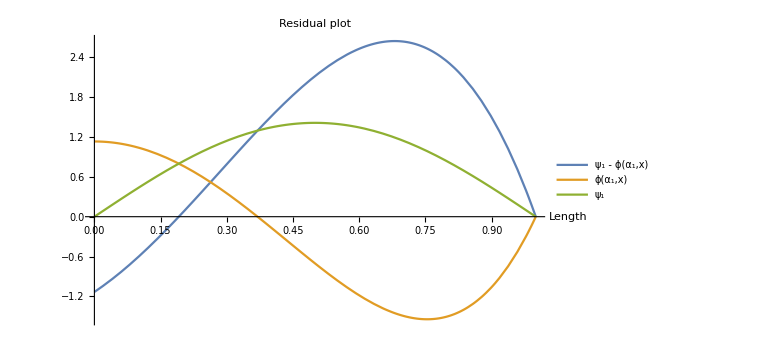

(*----------------------------------*)
(*Question 3: Gaussian Trial Function*)
(*----------------------------------*)

(1) Find normaliztion constant A of ϕ(r,α) = Ae^(-SuperscriptBox[αr, 2]) using procedures
in previous steps (i.e. Denominator is < ϕ | ϕ > =∫_(-∞)^∞ |ϕ|^2r^2dr = 1

(2) The normalization constant A therefore is A = (2 2^(3/4) α^(3/4))/π^(1/4)

(3) Numerator of E(α) = ∫_0^∞ ϕ^*Ĥϕr^2dr where Ĥ = -1/2(d/dr^2+2/rd/dr)-1/r

(4) Ĥϕ = -A/2(d/dr^2ϕ + 2/rd/drϕ) - ϕ/r = -(2 2^(3/4) ⅇ^(-r^2 α) α^(3/4) (1-3 r α+2 r^3 α^2))/(π^(1/4) r)

(5) Then E(α) = ∫_0^∞ -(8 ⅇ^(-2 r^2 α) √(2/π) α^(3/2) (1-3 r α+2 r^3 α^2))/r r^2dr

(6) E(α) = -2 √(2/π) √α+(3 α)/2

(7) Optimization of E(α) => (∂E (α))/(∂α) = 3/2-(√(2/π))/(√α) = 0

(8) Optimal parameter for α = 0.282942

(9) Minimum energy is E(α) = -0.424413. This
is a reasonable value since E_min in the textbook is the same constant (-0.424) times
m_e/(16 SuperscriptBox[π, 2] SuperscriptBox[SubscriptBox[ϵ, 0], 2] SuperscriptBox[ℏ, 2]) and E_0's constant is -0.500 times the m_e/(16 SuperscriptBox[π, 2] SuperscriptBox[SubscriptBox[ϵ, 0], 2] SuperscriptBox[ℏ, 2]) for Gaussian trial function
for H-atom

```mathematica
(*Jared Frazier*)
(*Variational-method-m6*)
(*Description:

Reproduction of variational principle findings from Physical Chemistry: A Molecular Approach (1997)
with demonstrated trial functions.

*)
(*Date: 11/18/2020*)
Clear["Global`*"]
(*-----------------------------------------------------*)
(*Question 1: Approximate Solution to Particle in 1D-box*)
(*-----------------------------------------------------*)

Print["
(*-----------------------------------------------------*)
(*Question 1: Approximate Solution to Particle in 1D-box*)
(*----------------------------------------------------*)"]
Print["(1) Find the normalization constant A and assume L = 1"]
Print["(2) Normalization constant can be be found by 
∫_0^L |ϕ|^2dx = 1 where ϕ = Ax(x-L)"]
Print["(3) Substituting ϕ into step (2), 
∫_0^L (Ax(x-L))^2dx = A^2∫_0^L x^2(x-L)^2dx = 1"]

(*Definite integral calculation*)
L = 1; (*Length of box*)
phi = A*x*(x-L); (*Phi trial function without normalization const*)
closedIntegralPhiSquare = Integrate[phi^2, {x, 0, L}]; (*Result of integral*)
(*/Definite integral calculation*)

Print["(4) Using Mathematica to calculate the definite integral
where L = 1, ", closedIntegralPhiSquare, " = 1"]
Print["(5) Normalization constant A therefore is A = +-√30"]
Print["(6)The Hamiltonian for a harmonic oscillator (particle
in a 1D-box) is given by Ĥ = -ℏ^2/(2  m)d^2/dx^2 + V(x) where V(x) = 0
in the bounds of the box 0 to L (L = 1)."]
Print["(7) E_ϕ = (< ϕ  |  OverscriptBox[H, ^]  |  ϕ >)/(< ϕ  |  ϕ >) = (∫_0^L)/(∫_0^L) =
= (∫_0^L)/1 =  (-FractionBox[SuperscriptBox[ℏ, 2], 2  m] SubsuperscriptBox[∫, 0, L]Ax (x - L) FractionBox[SuperscriptBox[d, 2], SuperscriptBox[dx, 2]] Ax (x - L) dx)/1"]

(*Second derivative of ϕ with respect to x and integral of phi*)
secondDerivPhi = D[phi, {x, 2}];
closedIntegralPhi = Integrate[phi, {x, 0, L}];
(*/Second derivative of ϕ with respect to x*)

Print["(8) The second derivative with respect to x of the integral
in the denominator of step (6) is ", secondDerivPhi, " 
then E_ϕ = (-2 A FractionBox[SuperscriptBox[ℏ, 2], 2  m] SubsuperscriptBox[∫, 0, L]Ax (x - L) dx)/1 where the integral is ", 
closedIntegralPhi, " then E_ϕ =(SuperscriptBox[A, 2] SuperscriptBox[ℏ, 2])/(6  m) = (30 SuperscriptBox[h, 2])/(24 SuperscriptBox[mπ, 2])"]

(*Calculation of Subscript[E, ϕ] and Subscript[E, o]*)
h = Quantity["PlanckConstant"]; (*J/s*)
electronMass = Quantity["ElectronMass"]; (*kg*) 
ePhi = (30*(h)^2)/(24*(electronMass)*Pi^2);
eNaught = (h)^2/(8*(electronMass));
(*/Calculation of Subscript[E, ϕ] and Subscript[E, 0]*)

Print["(9) Using mathematica, E_ϕ = ", N[ePhi, 4]]

Print["(10) This is a reasonable answer because E_ϕ > E_0, where E_0 = π^2/(2 SuperscriptBox[mL, 2]) = ", N[eNaught, 4] ]

(*Calculation of percent error*)
percentError =N[(ePhi - eNaught)/eNaught * 100, 4];
(*/Calculation of percent error*)

Print["(11) Therefore, E_ϕ = ", ePhi, " with ", percentError, "% error."]

(*---------------------------------------*)
(*Question 2: One parameter trial function*)
(*---------------------------------------*)
Print[
"\n(*---------------------------------------*)
(*Question 2: One parameter trial function*)
(*---------------------------------------*)"
]
Print["(1) First normalizing the function ϕ(α) = A(L^2- x^2)(L^2-αx^2) and using
∫_0^L |ϕ|^2dx = 1, therefore ∫_0^L (A(L^2- x^2)(L^2-αx^2))^2dx = 1"]

(*Normalization integral*)
phiAlpha = A*(L^2-x^2)(L^2-α*x^2); (*Without A*)
normIntegralPhiAlpha = Integrate[phiAlpha^2, {x, 0, L}];
(*/Normalization integral*)

Print["(2) Using Mathematica, the result of integration is
", normIntegralPhiAlpha, " = 1"]

(*Solve for A*)
normConstant = Solve[normIntegralPhiAlpha == 1, A];
positiveNormConstant = A/.normConstant[[2]];
phiAlphaOnly = positiveNormConstant*(L^2-x^2)*(L^2-α*x^2); (*In terms of alpha, x, and L only*)
(*/Solve for A*)

Print["(3) Using Mathematica, the normalization constant
is A = ", positiveNormConstant]
Print["(4) Knowing the normalization constant,
E(α) = (< ϕ (α)  |  OverscriptBox[H, ^]  |  ϕ (α) >)/(< ϕ (α)  |  ϕ (α) >) = (∫_0^L)/(∫_0^L) = ∫_0^L (ϕ(α))^*Ĥϕ(α)dx"]
Print["(5) Ĥ = -ℏ^2/(2  m)d^2/dx^2 + V(x) but V(x) = 0 in the 1D box, so substituting
Ĥ and ϕ(α) into step (4), E(α) = -ℏ^2/(2  m)∫_0^L ", phiAlphaOnly," d^2/dx^2", phiAlphaOnly, " dx"]

(*Second derivative of ϕ with respect to x and integral of phiAlpha*)
secondDerivPhiAlpha = D[phiAlphaOnly, {x, 2}];
(*/Second derivative of ϕ with respect to x and integral of phiAlpha*)

Print["(5) Second derivative inside the integrand is 
d^2/dx^2", phiAlphaOnly, " = ",  Simplify[secondDerivPhiAlpha], " The integral now becomes
E(α) = -ℏ^2/(2  m)∫_0^L ", Simplify[phiAlphaOnly*secondDerivPhiAlpha], "dx"]

(*Solution to integral*)
phiAlphaIntegrand = phiAlphaOnly*secondDerivPhiAlpha;
integralPhiAlpha = Integrate[phiAlphaIntegrand, {x, 0, L}];
(*/Solution to integral*)

Print["(6) The result of that integral is E(α) = ", Simplify[-h^2/(8*electronMass*Pi^2)* integralPhiAlpha]]

(*Derivative ePhi with respect to α set to 0*)
eAlpha = -h^2/(8*electronMass*Pi^2) * integralPhiAlpha;
eAlphaFunc[α_] = -h^2/(8*electronMass*Pi^2) * integralPhiAlpha;
derivEAlpha = D[eAlpha, {α, 1}];
optimizedEAlpha = NSolve[derivEAlpha == 0, α];
alphaOne = α/.optimizedEAlpha[[1]];
alphaTwo = α/.optimizedEAlpha[[2]];
(*/Derivative ePhi with respect to α set to 0*)

Print["(7) Then optimizing the parameter α, (∂E (α))/(∂α) = ", Simplify[derivEAlpha], " = 0" ]
Print["(8) α_1 = ", N[alphaOne, 3], " or α_2 = ", N[alphaTwo, 3]];
Print["(9) For α_1 = ", N[alphaOne, 3], " E(α_1) = ", eAlphaFunc[alphaOne]]
Print["    For α_2 = ", N[alphaTwo, 3], " E(α_1) = ", eAlphaFunc[alphaTwo]]

(*%error both instances*)
percentErrorAlpha1 = (eAlphaFunc[alphaOne] - eNaught)/eNaught*100;
(*/%error both instances*)

Print["(10) The optimal parameter value for this function must therefore be
α_1= ", alphaOne, " with corresponding energy E(α_1) = ", eAlphaFunc[alphaOne]]

(*Residual Plot*)
exactPsi = Sqrt[2]*Sin[Pi*x];
phiOptimalAlphaOnly = phiAlphaOnly/.α->alphaOne;
Plot[
	{exactPsi-phiOptimalAlphaOnly, phiOptimalAlphaOnly, 
	exactPsi},
	{x, 0, L}, PlotLabel->"Residual plot",
	AxesLabel->{"Length"}, PlotRange->Full, ImageSize->Large,
	PlotLegends->{"ψ_1 - ϕ(α_1,x)", "ϕ(α_1,x)", "ψ_1"}
]
(*----------------------------------*)
(*Question 3: Gaussian Trial Function*)
(*Pg 382 MCQ 2e*)
(*----------------------------------*)
Print[
"\n(*----------------------------------*)
(*Question 3: Gaussian Trial Function*)
(*----------------------------------*)"
]
Print["(1) Find normaliztion constant A of ϕ(r,α) = Ae^(-SuperscriptBox[αr, 2]) using procedures
in previous steps (i.e. Denominator is < ϕ | ϕ > =∫_(-∞)^∞ |ϕ|^2r^2dr = 1"]

(*Normalize the Gaussian*)
gaussian = A*Exp[-1*α*r^2]; (*Gaussian trial function*)
gaussianNormalizationIntegral = Normal[Integrate[r^2*gaussian^2, {r, 0, Infinity}]];
gaussianNormalizationConst = Simplify[A/.(Solve[gaussianNormalizationIntegral == 1, A])[[2]]];
normalizedGaussian = gaussian/.A->gaussianNormalizationConst;
(*/Normalize the Gaussian*)

Print["(2) The normalization constant A therefore is A = ", gaussianNormalizationConst]
Print["(3) Numerator of E(α) = ∫_0^∞ ϕ^*Ĥϕr^2dr where Ĥ = -1/2(d/dr^2+2/rd/dr)-1/r"]

(*Hamiltonian operator*)
secondDerivGaussian = D[normalizedGaussian, {r, 2}];
firstDerivGaussian = D[normalizedGaussian, {r, 1}];
divRGaussian = normalizedGaussian/r;
hamiltonianOnGaussian = -1/2*(secondDerivGaussian+2/r*firstDerivGaussian) - divRGaussian;
(*/Hamilitonian operator*)

Print["(4) Ĥϕ = -A/2(d/dr^2ϕ + 2/rd/drϕ) - ϕ/r = ", Simplify[hamiltonianOnGaussian]]
Print["(5) Then E(α) = ∫_0^∞ ", Simplify[normalizedGaussian*hamiltonianOnGaussian], " r^2dr"]

(*Evaluate Hamiltonian with L = Infinity for hydrogen*)
eHAtom = Simplify[Normal[Integrate[normalizedGaussian*hamiltonianOnGaussian*r^2, {r, 0, Infinity}]]];
(*/Evaluate Hamiltonian with L = Infinity for hydrogen*)

Print["(6) E(α) = ", eHAtom]

(*Optimize E(α)*)
firstDerivEHAtom = D[eHAtom, {α, 1}];
optimizedEHAtom = NSolve[firstDerivEHAtom == 0, α];
alphaEHAtom = α/.optimizedEHAtom[[1]];
functionEHAtom[a_] = -2*Sqrt[2/Pi]*Sqrt[a]+(3*a/2);
(*/Optimize E(α)*)
Print["(7) Optimization of E(α) => (∂E (α))/(∂α) = ", firstDerivEHAtom, " = 0"]
Print["(8) Optimal parameter for α = ", alphaEHAtom]
Print["(9) Minimum energy is E(α) = ", functionEHAtom[alphaEHAtom], ". This
is a reasonable value since E_min in the textbook is the same constant (-0.424) times
m_e/(16 SuperscriptBox[π, 2] SuperscriptBox[SubscriptBox[ϵ, 0], 2] SuperscriptBox[ℏ, 2]) and E_0's constant is -0.500 times the m_e/(16 SuperscriptBox[π, 2] SuperscriptBox[SubscriptBox[ϵ, 0], 2] SuperscriptBox[ℏ, 2]) for Gaussian trial function
for H-atom"]
```